TROJITÁ GEOMETRICKÁ TRANSFORMÁCIA BODU

==========================================

POČIATOČNÝ BOD:

Súradnice bodu P:

P = (-1
2)

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: II

PRVÁ TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE BODU - POSUN

========================================

ZADANIE:

Majme bod P so súradnicami:

(-1
2)

Vykonajte posun bodu v 2D priestore pomocou vektora posunu: Δ = [-3, -3]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | -3
0 | 1 | -3
0 | 0 | 1)

POSTUP:

Pre výpočet použijeme maticu posunu v homogénnych súradniciach:

Transformačná matica:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Pre naše hodnoty:

dx = -3

dy = -3

Posun vykonáme pomocou vzorcov:

x' = x + dx

y' = y + dy

Výpočet pre bod P:

Pôvodné súradnice: [-1, 2]

Výpočet x-ovej súradnice:

x' = x + dx = -1 + -3

x' = -4

Výpočet y-ovej súradnice:

y' = y + dy = 2 + -3

y' = -1

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -4 + (3) = -1

y = y' + (-dy) = -1 + (3) = 2

Maticový zápis:

(1 | 0 | -3
0 | 1 | -3
0 | 0 | 1) · (-1
2
1) = (-4
-1
1)

VÝSLEDOK:

Súradnice bodu po posune:

(-4
-1)

VIZUALIZÁCIA:

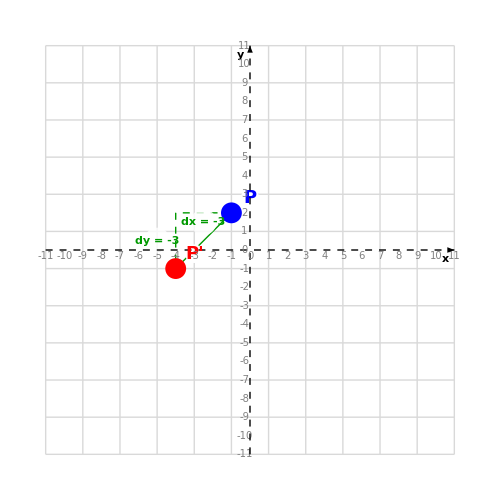

LEGENDA:

• Modrý bod: Pôvodný bod P

• Červený bod: Posunutý bod P'

• Zelená šípka: Vektor posunu

• Zelené prerušované čiary: Posun po súradniciach

• Mriežka: Súradnicový systém

Pôvodný bod (modrá):

Bod P: {-1,2}

Výsledný bod (červená):

Bod P': {-4,-1}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [3, 3] (opačný vektor)

DRUHÁ TRANSFORMÁCIA: Rotácia

GEOMETRICKÉ TRANSFORMÁCIE BODU - ROTÁCIA

========================================

ZADANIE:

Majme bod P so súradnicami:

P = (-4
-1)

Vykonajte rotáciu bodu v 2D priestore okolo počiatku súradnicovej sústavy [0,0] o uhol α = 150°.

Transformačná matica rotácie:

(-(√3)/2 | -1/2
1/2 | -(√3)/2)

POSTUP:

Pre výpočet použijeme maticu rotácie:

Transformačná matica:

(cos(α) | -sin(α)
sin(α) | cos(α))

Naša hodnotu α = 150°:

cos(α) = -1/2 · √3

sin(α) = 1/2

Rotáciu vykonáme pomocou vzorcov:

x' = x · cos(α) - y · sin(α)

y' = x · sin(α) + y · cos(α)

Výpočet pre bod P:

Pôvodné súradnice: [-4, -1]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -4 · -1/2 · √3 - -1 · 1/2

x' = 1/2 + 2 · √3

x' = 1/2 + 2 · √3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -4 · 1/2 + -1 · -1/2 · √3

y' = -2 + √3/2

y' = (-4 + √3)/2

Výsledné súradnice: [1/2 + 2 · √3, -2 + √3/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -150°:

cos(α') = -1/2 · √3

sin(α') = -1/2

x = x' · cos(α') - y' · sin(α')

x = 1/2 + 2 · √3 · -1/2 · √3 - (-4 + √3)/2 · -1/2

x = -4

x = -4 = -4

y = x' · sin(α') + y' · cos(α')

y = 1/2 + 2 · √3 · -1/2 + (-4 + √3)/2 · -1/2 · √3

y = -1

y = -1 = -1

Maticový zápis:

(-(√3)/2 | -1/2
1/2 | -(√3)/2) · (-4
-1) = (1/2+2 √3
-2+(√3)/2)

VÝSLEDOK:

Súradnice bodu po rotácii:

P' = (1/2+2 √3
-2+(√3)/2)

VIZUALIZÁCIA:

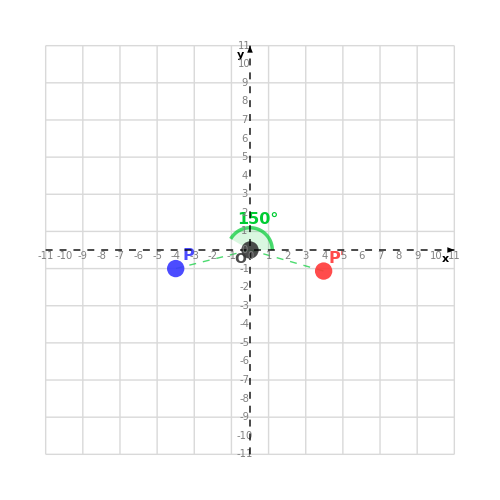

LEGENDA:

• Modrý bod: Pôvodný bod P

• Červený bod: Otočený bod P'

• Zelený oblúk: Znázornenie uhlu rotácie

• Zelené prerušované čiary: Spojenia bodov s počiatkom

• Mriežka: Súradnicový systém

• O: Počiatok súradnicovej sústavy - stred rotácie

Pôvodné súradnice (modrá):

Bod P: {-4,-1}

Výsledné súradnice (červená):

Bod P': {1/2+2 √3,-2+(√3)/2}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite rotáciu o opačný uhol:

α' = -α = -150°

MATEMATICKÉ VLASTNOSTI:

• Rotácia okolo počiatku zachováva vzdialenosť bodu od počiatku sústavy [0,0]

• Rotácia je izometrická transformácia - zachováva vzdialenosti

• Rotácia zachováva uhly medzi úsečkami a ich dĺžky

• Počiatok súradnicovej sústavy [0,0] je fixný bod rotácie - zostáva nezmenený

• Ak bod P leží na kruhu so stredom v počiatku, po rotácii zostáva na tom istom kruhu

TABUĽKA ŠPECIÁLNYCH HODNÔT:

Hodnoty pre najčastejšie uhly:

α | sin(α) | cos(α)
0° | 0 | 1
30° | 1/2 | √3/2
45° | 1/√2 | 1/√2
60° | √3/2 | 1/2
90° | 1 | 0
120° | √3/2 | -1/2
135° | 1/√2 | -1/√2
150° | 1/2 | -√3/2
180° | 0 | -1
270° | -1 | 0
360° | 0 | 1

TRETIA TRANSFORMÁCIA: Zväčšenie/Zmenšenie

GEOMETRICKÉ TRANSFORMÁCIE BODU - ZVÄČŠENIE/ZMENŠENIE

========================================

ZADANIE:

Majme bod P so súradnicami:

P = (1/2+2 √3
-2+(√3)/2)

Vykonajte zmenšenie bodu pomocou transformačnej matice v 2D priestore:

(1/2 | 0
0 | 1/2)

POSTUP:

Pre výpočet použijeme maticu zmenšenie v tvare:

Transformačná matica:

(sx | 0
0 | sy)

kde:

sx je koeficient zmenšenie v smere osi x

sy je koeficient zmenšenie v smere osi y

V našom prípade:

sx = 1/2 (zmenšovanie v smere osi x)

sy = 1/2 (zmenšovanie v smere osi y)

Výpočet pre bod P:

Pôvodné súradnice: [1/2 + 2 · √3, -2 + √3/2]

Výpočet x-ovej súradnice:

x' = sx · x = 1/2 · 1/2 + 2 · √3

x' = 1/4 + √3

x' = 1/4 + √3

Výpočet y-ovej súradnice:

y' = sy · y = 1/2 · -2 + √3/2

y' = -1 + √3/4

y' = (-4 + √3)/4

Výsledné súradnice: [1/4 + √3, (-4 + √3)/4]

Overenie pomocou inverznej transformácie:

x = x'/sx = 1/4 + √3/1/2 = 2 · (1/4 + √3)

y = y'/sy = (-4 + √3)/4/1/2 = (-4 + √3)/2

Maticový zápis:

(1/2 | 0
0 | 1/2) · (1/2+2 √3
-2+(√3)/2) = (1/4+√3
1/4 (-4+√3))

VÝSLEDOK:

Súradnice bodu po zmenšenie:

P' = (1/4+√3
-1+(√3)/4)

VIZUALIZÁCIA:

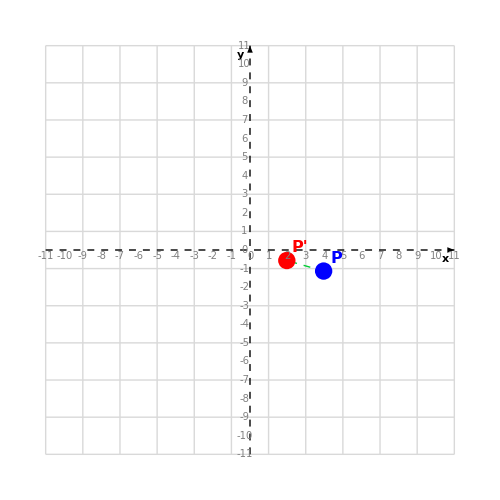

LEGENDA:

• Modrý bod: Pôvodný bod P

• Červený bod: Bod po zmenšenie

• Zelená prerušovaná čiara: Dráha zmeny veľkosti bodu

• Mriežka: Súradnicový systém

Pôvodné súradnice (modrá):

Bod P: {1/2+2 √3,-2+(√3)/2}

Výsledné súradnice (červená):

Bod P': {1/4+√3,-1+(√3)/4}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite koeficienty:

sx' = 1/sx = 2 (zväčšovanie v smere osi x)

sy' = 1/sy = 2 (zväčšovanie v smere osi y)

MATEMATICKÉ VLASTNOSTI:

• Pri rovnakých koeficientoch (sx = sy = 1/2):

- Proporcionálne zmenšenie bodu od počiatku súradnicovej sústavy

- Vzdialenosti od počiatku sa zmenšujú na 2. časť

• Body ležiace na osi x sa približujú od počiatku v smere osi x

• Body ležiace na osi y sa približujú od počiatku v smere osi y

• Bod [0,0] (počiatok súradnicovej sústavy) zostáva nezmenený

ŠPECIÁLNE PRÍPADY:

• Ak sx = sy = 1, k zmene nedôjde (identická transformácia)

• Ak sx = sy, ide o proporcionálne zmenšenie bodu

• Ak sx = 1, bod sa posunúva len v smere osi y

• Ak sy = 1, bod sa posunúva len v smere osi x

• Ak sx = -1, bod sa zrkadlí podľa osi y

• Ak sy = -1, bod sa zrkadlí podľa osi x

POSTUPNÝ VÝPOČET:

Pôvodný bod P:

Súradnice:

{-1,2}

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: II

Po prvej transformácii (Posun):

Súradnice bodu P':

{-4,-1}

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: III

Po druhej transformácii (Rotácia):

Súradnice bodu P'':

{1/2+2 √3,-2+(√3)/2}

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: IV

Po tretej transformácii (Zväčšenie/Zmenšenie):

Súradnice bodu P''':

{1/4+√3,-1+(√3)/4}

Vlastnosti bodu:

Vzdialenosť od počiatku: 10

Kvadrant: IV

SÚHRNNÁ VIZUALIZÁCIA:

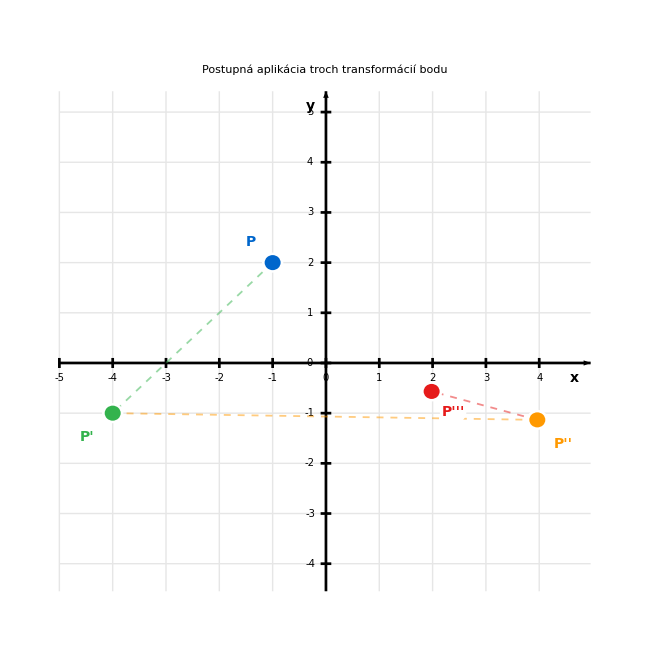

LEGENDA:

• Modré body: Pôvodný bod P

• Tmavozelené body: Bod P' po prvej transformácii (Posun)

• Oranžové body: Bod P'' po druhej transformácii (Rotácia)

• Červené body: Bod P''' po tretej transformácii (Zväčšenie/Zmenšenie)

Postupnosť transformácií:

1. Posun

2. Rotácia

3. Zväčšenie/Zmenšenie

ZÁVEREČNÝ PREHĽAD:

Vykonali ste postupne tieto transformácie:

1. Posun

2. Rotácia

3. Zväčšenie/Zmenšenie

Výsledný bod P''':

(1/4+√3
1/4 (-4+√3))

```mathematica
BodTrojitaTransformaciaSVysledkom[]
```